Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zmm=(GetYodaRaw[NotebookDirectory[]<>"Zmm.yoda"]);
ATLAS=(GetYodaRaw[NotebookDirectory[]<>"ATLAS_Zmm.yoda"]);
```

1 Imported ..Histo1D..  /ATLAS_1407_3935/Mmm/0

1 Imported ..Scatter2D..  /REF/ATLAS_1008_2461/d01-x01-y01

OptionValue::nodef: Unknown option "PlotStyle" for HistogramPlot.

Rescaling Histogram y-Axis with 2.4

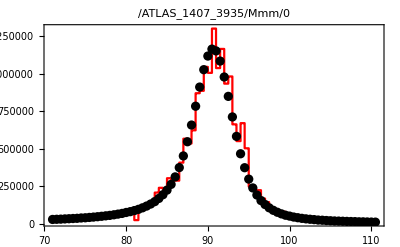

```mathematica
F1=HistogramPlot[Zmm[[1]],HistScale->2.4,PlotStyle->{Red}];
F2=ScatterPlot[ATLAS[[1]],PlotStyle->{Black}];
Show[{F1,F2}]
```